## Page-Wootters model: NN-level clock + 2-level system

```mathematica
NN= 60
```

60

```mathematica
T := DiagonalMatrix[Range[0,NN-1]]
```

```mathematica
F := FourierMatrix[NN]
```

```mathematica
Ω := F.T.F†
```

Hamiltonian in "ordinary" space

```mathematica
Hs := ⅈ{{0,1},{-1,0}}
```

```mathematica
MatrixForm[Hs]
```

(0 | ⅈ
-ⅈ | 0)

Matrix representation of eq. (1) in https://arxiv.org/abs/1504.04215 by Lloyd, Giovannetti and Maccone.
We turn it into numeric as treating  it symbolically onwards would be unfeasible.

```mathematica
J := N[KroneckerProduct[Ω,IdentityMatrix[2]] + KroneckerProduct[IdentityMatrix[NN],Hs]]
```

```mathematica
Chop[Eigenvalues[J]]
```

{60.,59.,58.,58.,57.,57.,56.,56.,55.,55.,54.,54.,53.,53.,52.,52.,51.,51.,50.,50.,49.,49.,48.,48.,47.,47.,46.,46.,45.,45.,44.,44.,43.,43.,42.,42.,41.,41.,40.,40.,39.,39.,38.,38.,37.,37.,36.,36.,35.,35.,34.,34.,33.,33.,32.,32.,31.,31.,30.,30.,29.,29.,28.,28.,27.,27.,26.,26.,25.,25.,24.,24.,23.,23.,22.,22.,21.,21.,20.,20.,19.,19.,18.,18.,17.,17.,16.,16.,15.,15.,14.,14.,13.,13.,12.,12.,11.,11.,10.,10.,9.,9.,8.,8.,7.,7.,6.,6.,5.,5.,4.,4.,3.,3.,2.,2.,1.,1.,-1.,0}

```mathematica
chosenEigenvector := Eigenvectors[J][[ 100]]

chosenProbUnnormalized := Abs[chosenEigenvector^2]
```

```mathematica
Normalization := chosenProbUnnormalized[[1]] + chosenProbUnnormalized[[2]]
```

```mathematica
probability := chosenProbUnnormalized / Normalization
```

```mathematica
probability
```

{0.0691856,0.930814,0.0779041,0.922096,0.10507,0.89493,0.149496,0.850504,0.209242,0.790758,0.281694,0.718306,0.363688,0.636312,0.451639,0.548361,0.541704,0.458296,0.629946,0.370054,0.712509,0.287491,0.785784,0.214216,0.846569,0.153431,0.892207,0.107793,0.920704,0.0792959,0.930814,0.0691856,0.922096,0.0779041,0.89493,0.10507,0.850504,0.149496,0.790758,0.209242,0.718306,0.281694,0.636312,0.363688,0.548361,0.451639,0.458296,0.541704,0.370054,0.629946,0.287491,0.712509,0.214216,0.785784,0.153431,0.846569,0.107793,0.892207,0.0792959,0.920704,0.0691856,0.930814,0.0779041,0.922096,0.10507,0.89493,0.149496,0.850504,0.209242,0.790758,0.281694,0.718306,0.363688,0.636312,0.451639,0.548361,0.541704,0.458296,0.629946,0.370054,0.712509,0.287491,0.785784,0.214216,0.846569,0.153431,0.892207,0.107793,0.920704,0.0792959,0.930814,0.0691856,0.922096,0.0779041,0.89493,0.10507,0.850504,0.149496,0.790758,0.209242,0.718306,0.281694,0.636312,0.363688,0.548361,0.451639,0.458296,0.541704,0.370054,0.629946,0.287491,0.712509,0.214216,0.785784,0.153431,0.846569,0.107793,0.892207,0.0792959,0.920704}

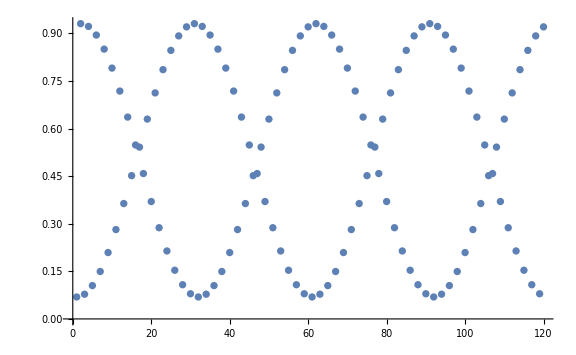

```mathematica
ListPlot[probability, GridLines ->{Range[0,NN*2, 2], Range[0,1,0.1]}, ImageSize->Large]
```

Consistency of PW with ordinary QM (discrete approximation):

Ordinary quantum mechanics time evolution, with initial state  (1-i)/2 * |0>  + (1+i)/2 |1>

```mathematica
psi[t_] := MatrixExp[-ⅈ Hs t, {(1/2)-(1/2)ⅈ,(1/2)+(1/2)ⅈ} ]
```

```mathematica
psi[t]
```

{(1/2-ⅈ/2) Cos[t]+(1/2+ⅈ/2) Sin[t],(1/2+ⅈ/2) Cos[t]-(1/2-ⅈ/2) Sin[t]}

Picking 8 samples, equally spaced from 0 to 2π (excluding 2π)

```mathematica
Map[psi, Range[0,(7/4)π,π/4]]
```

{{1/2-ⅈ/2,1/2+ⅈ/2},{1/(√2),ⅈ/(√2)},{1/2+ⅈ/2,-1/2+ⅈ/2},{ⅈ/(√2),-1/(√2)},{-1/2+ⅈ/2,-1/2-ⅈ/2},{-1/(√2),-ⅈ/(√2)},{-1/2-ⅈ/2,1/2-ⅈ/2},{-ⅈ/(√2),1/(√2)}}

This discrete time evolution (samples from an ordinary QM result) coincides with the eigenvector of J related to eigenvalue 0 (PW model result).

```mathematica
Eigensystem[Hs]
```

{{-1,1},{{-ⅈ,1},{ⅈ,1}}}